```mathematica
L=8.29015544041451*^7;
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k0_?NumberQ,α_?NumberQ,β_?NumberQ,γ_?NumberQ]:=foo[s,k0,α,β,γ]
```

```mathematica
foo[s_/;(s^2==1),k0_?NumberQ,α_?NumberQ,β_?NumberQ,γ_?NumberQ]:=Module[{bl,b,g,m31,m32,m33,m34,xl,xr},
g=1/Sqrt[2]({{1-s}, {1+s}, {k0(1-s)}, {k0(1+s)}});

{m31,m32,m33,m34}=n/.Solve[(k0^2/q^2(-2 β^2+2 α γ)-(n-2)^2 α-(n)^2 γ)^2==((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ),n];
U[z_]:=({{ⅇ^(ⅈ m31 q z), ⅇ^(ⅈ m32 q z), ⅇ^(ⅈ m33 q z), ⅇ^(ⅈ m34 q z)}, {(q^2 m31^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m31-2) q z), (q^2 m32^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m32-2) q z), (q^2 m33^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m33-2) q z), (q^2 m34^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m34-2) q z)}, {m31 q ⅇ^(ⅈ m31 q z), m32 q ⅇ^(ⅈ m32 q z), m33 q ⅇ^(ⅈ m33 q z), m34 q ⅇ^(ⅈ m34 q z)}, {(q^2 m31^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m31-2) q z)(m31-2) q, (q^2 m32^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m32-2) q z)(m32-2) q, (q^2 m33^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m33-2) q z)(m33-2) q, (q^2 m34^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m34-2) q z)(m34-2) q}});
U0=1/Sqrt[2]({{0, 2, -2, 0}, {2, 0, 0, -2}, {0, 2k0, 2k0, 0}, {2k0, 0, 0, 2k0}});
T=({{ⅇ^(-ⅈ k0 L), 0, 0, 0}, {0, ⅇ^(-ⅈ k0 L), 0, 0}, {0, 0, ⅇ^(ⅈ k0 L), 0}, {0, 0, 0, ⅇ^(ⅈ k0 L)}});

b=Inverse[U[0]].g;
bl=Inverse[T].Inverse[U0].U[-L].b;

{{m31,m32,m33,m34},bl}]
```

```mathematica
CoeffLinComb2[k0_?NumberQ,α_?NumberQ,β_?NumberQ,γ_?NumberQ,in_]:=Module[{bl,b,g,gg,m31,m32,m33,m34,res,hp,hm,xl,xr,trans,ref},
bl={in[[1]],in[[2]],hp,hm};
gg=xl/Sqrt[2]({{0}, {2}, {0}, {k0/q 2}})+xr/Sqrt[2]({{2}, {0}, {k0/q 2}, {0}});
{m31,m32,m33,m34}=n/.Solve[(k0^2/q^2(-2 β^2+2 α γ)-(n-2)^2 α-(n)^2 γ)^2==((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ),n];
U[z_]:=({{ⅇ^(ⅈ m31 q z), ⅇ^(ⅈ m32 q z), ⅇ^(ⅈ m33 q z), ⅇ^(ⅈ m34 q z)}, {(q^2 m31^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m31-2) q z), (q^2 m32^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m32-2) q z), (q^2 m33^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m33-2) q z), (q^2 m34^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m34-2) q z)}, {m31  ⅇ^(ⅈ m31 q z), m32  ⅇ^(ⅈ m32 q z), m33  ⅇ^(ⅈ m33 q z), m34  ⅇ^(ⅈ m34 q z)}, {(q^2 m31^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m31-2) q z)(m31-2), (q^2 m32^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m32-2) q z)(m32-2), (q^2 m33^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m33-2) q z)(m33-2), (q^2 m34^2-α k0^2)/(β k0^2)ⅇ^(ⅈ (m34-2) q z)(m34-2)}});
U0=1/Sqrt[2]({{0, 2, -2, 0}, {2, 0, 0, -2}, {0, 2 k0/q, 2 k0/q, 0}, {2 k0/q, 0, 0, 2 k0/q}});
T=({{ⅇ^(-ⅈ k0 L), 0, 0, 0}, {0, ⅇ^(-ⅈ k0 L), 0, 0}, {0, 0, ⅇ^(ⅈ k0 L), 0}, {0, 0, 0, ⅇ^(ⅈ k0 L)}});


b=Inverse[U[-L]].U0.T.bl;

res={xl,xr,hp,hm}/.Solve[U[0].b==gg,{hp,hm,xl,xr}];
{xl,xr,hp,hm}={res[[1]][[1]],res[[1]][[2]],res[[1]][[3]],res[[1]][[4]]};
trans=Abs[xl]^2+Abs[xr]^2;
ref = Abs[hp]^2+Abs[hm]^2;

{xl,xr,hp,hm,trans,ref}](*первые 4 аргументы амплитуды при соответсвующих поляризациях отраженной и прошедших волн,5 и 6 коэффициенты прохождения и отражения *)
```

Проверка унитарности. В данном случае одна из поляризации слева нормирована на 1. В конечном варианте нужно будет перенормировать на поляризацию справа, т.е. разделить все на Abs[ce2[[1]]]^2+Abs[ce2[[2]]]^2

```mathematica
ce2=CoeffLinComb2[1,2,1,0.5,1,{1,0}]
Abs[ce2[[1]]]^2+Abs[ce2[[2]]]^2+Abs[ce2[[3]]]^2+Abs[ce2[[4]]]^2
ce2[[5]]+ce2[[6]]
```

{-0.591379+0.754571 ⅈ,-0.2254-0.0138731 ⅈ,0.1037+0.102801 ⅈ,-0.0126775-0.0917222 ⅈ,0.970105,0.0298954}

1.

1.

Коэффициент прохождения для падающее правой волны

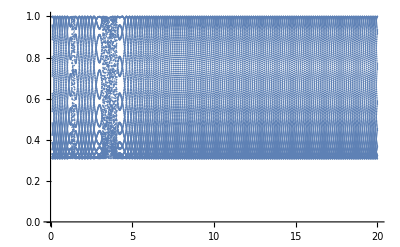

```mathematica
t=ParallelTable[{k0,Abs[CoeffLinComb2[k0,1,0.01,0.2,{1,0}][[5]]]^2},{k0,0.1,20,0.0005}];
ListPlot[t]
```